## Scientific Programming 7

## Compiling a function

Consider the z^3-1=0. Apply the Newton iteration to this and get: w_(n+1) = 2(2 w_n + 1/((w^2)_n)). To which root does this converge given some initial value?

```mathematica
whichroot[z_,n_]:=
Module[{w=N[z]},
Do[w=1/3(2w+1/w^2),{n}];
Which[Re[w]>0,0,Im[w]>0,1,True,2] (*Which is an extended form of If*)
           ]
```

```mathematica
?Which
```

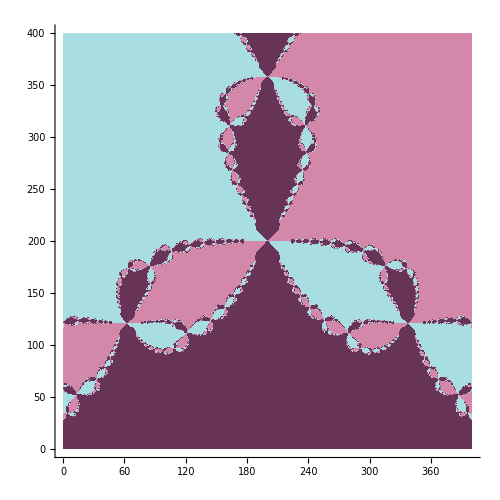
{4.46875,-Graphics-}

```mathematica
Timing[
ArrayPlot[
Table[whichroot[x+ⅈ y,10],{x,-1,1,2./399},{y,-1,1,2./399}],
ImageSize->500,
ColorFunction->"CandyColors",
Axes-> True]]
```

We can compile this function, which makes it a lot faster!

```mathematica
cwhichroot=
Compile[{{z, _Complex},{n, _Integer}}, 
Module[{w=N[z]},
Do[w=1/3(2w+1/w^2),{n}];
Which[Re[w]>0,0,Im[w]>0,1,True,2]
           ]]
```

CompiledFunction[…]

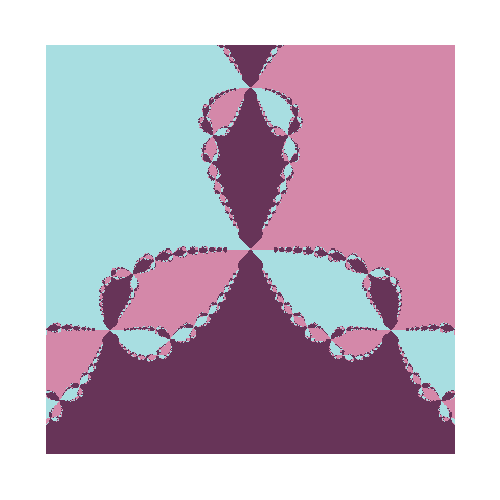
{0.546875,-Graphics-}

```mathematica
Timing[
ArrayPlot[
Table[cwhichroot[x+ⅈ y,10],{x,-1,1,2./399},{y,-1,1,2./399}],
ImageSize->500,
ColorFunction->"CandyColors"]]
```

```mathematica
Timing[
ArrayPlot[
Table[cwhichroot[x+ⅈ y,10],{x,-1,1,2./999},{y,-1,1,2./999}],
ImageSize->600,
ColorFunction->"CandyColors"]]
```

{3.21875,-Graphics-}

We can both compile are parallelize, but in this case it doesn’t make much of a difference.

```mathematica
pcwhichroot=
Compile[{{z, _Complex},{n, _Integer}}, 
Module[{w=N[z]},
Do[w=1/3(2w+1/w^2),{n}];
Which[Re[w]>0,0,Im[w]>0,1,True,2]
           ],
RuntimeAttributes->{Listable},
Parallelization->True
                ]
```

CompiledFunction[…]

```mathematica
Timing[
ArrayPlot[
Table[pcwhichroot[x+ⅈ y,10],{x,-1,1,2./999},{y,-1,1,2./999}],
ImageSize->600,
ColorFunction->"CandyColors"]]
```

{3.20313,-Graphics-}

## Hard Equations

```mathematica
SetDirectory["/Users/old philip/Bureaucracy/Mathematical Institute/Courses/Mathematica Course/mathfiles/Hard Equations/"];
```

```mathematica
hardeqs=
SortBy[
Rest[<<"/Users/old philip/Bureaucracy/Mathematical Institute/Courses/Mathematica Course/mathfiles/Hard Equations/hardEquations.nb"],Length];
```

```mathematica
Length[hardeqs]
```

65526

This tells us how many variables there are.

```mathematica
clist=Variables[hardeqs];
```

```mathematica
Length[clist]
```

30581

```mathematica
Take[hardeqs,10]//Column
```

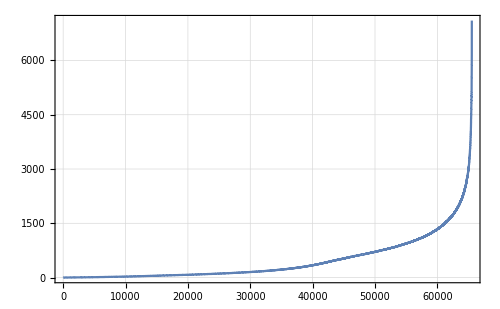

```mathematica
ListPlot[Length/@hardeqs,
PlotRange->All,
Joined->True,
Frame->True,
GridLines->Automatic,
ImageSize->500]
```

```mathematica
hardeqs⟦100⟧
```

-c[4810]-c[4835]

```mathematica
hardeqs⟦500⟧
```

c[29131]+c[29158]

```mathematica
hardeqs⟦5000⟧
```

c[11993]+c[11994]-c[11997]-c[12070]-c[14443]-c[14444]+c[14447]+c[14520]-c[24418]-c[24419]+c[24422]+c[24495]

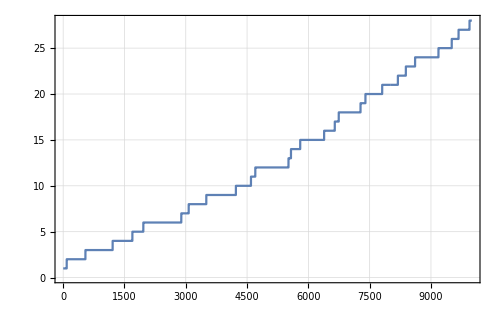

```mathematica
ListPlot[Length/@Take[hardeqs,10000],
PlotRange->All,
Joined->True,
Frame->True,
GridLines->Automatic,
ImageSize->500]
```

Apparently the solutions are supposed to be integers, but Solve doesn’t work. NSolve will give a solutions, but probably a trivial one. It is usually good to solve mod p (prime), for many p, and then use Chinese remainder theorem to reconstruct the answers.

```mathematica
simp[ls_]:=
SortBy[
Simplify[ls],Length]

solnsimp[sol_]:=
SortBy[
Simplify[sol],Length[Last[#]]&] (*Simplify the output which is generally like List[Rule[Subscript[c, 1],Subscript[c, 2]+Subscript[c, 3]],...]*)

(*Idea: solve chunks of equations*)
chunksolve[eqs_,chunksize_]:=
Module[{n,chunks,currentsoln={},nextsoln, tim},
chunks=Partition[eqs,UpTo[chunksize]];(*UpTo allows one chunk that is shorter as size might not be multiple of chunksize*)
Do[nextsoln=solnsimp[ Solve[simp[ chunks⟦n⟧/.currentsoln ]==0]⟦1⟧];
     {tim,currentsoln}=AbsoluteTiming[ If[n==1,nextsoln,solnsimp[ Join[currentsoln/.nextsoln,nextsoln] ] ] ];
     currentsoln>>currentsoln.nb; (*Write to a file - if you abort, you still get some results*)
     Print[n," )   ", tim," Sec,   Length[currentlist] = ", Length[currentsoln]],
    {n,1,Ceiling[Length[eqs]/chunksize]} ]
             ]
```

```mathematica
chunksolve[hardeqs,1000]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

1 )   2.×10^-6 Sec,   Length[currentlist] = 860

2 )   0.662272 Sec,   Length[currentlist] = 1630

3 )   1.89028 Sec,   Length[currentlist] = 2351

4 )   6.15191 Sec,   Length[currentlist] = 3062

5 )   15.4501 Sec,   Length[currentlist] = 3738

6 )   53.0874 Sec,   Length[currentlist] = 4377

$Aborted

Note that this becomes rather slow (time increases by about a factor of 3 or so). Simplify is a rather time consuming function, so let’s use ExpandAll instead.

```mathematica
simp[ls_]:=
SortBy[
ExpandAll[ls],Length]

solnsimp[sol_]:=
SortBy[
ExpandAll[sol],Length[Last[#]]&]

Off[Solve::svars]

chunksolve[eqs_,chunksize_]:=
Module[{n,chunks,currentsoln={},nextsoln, nexttim,simptim},
chunks=Partition[eqs,UpTo[chunksize]];
Do[{nexttim,nextsoln}=AbsoluteTiming[ solnsimp[ Solve[simp[ chunks⟦n⟧/.currentsoln ]==0]⟦1⟧] ];
     {simptim,currentsoln}=AbsoluteTiming[If[n==1,nextsoln,solnsimp[ Join[currentsoln/.nextsoln,nextsoln] ] ] ];
     currentsoln>>currentsoln.nb; Print[n,")   nexttim = ", nexttim," Sec,   simptim = ", simptim, "   Length[currentsoln] = ", Length[currentsoln]],
    {n,1,Ceiling[Length[eqs]/chunksize]} ]
             ]
```

```mathematica
chunksolve[hardeqs,1000]
```

1)   nexttim = 0.376497 Sec,   simptim = 2.×10^-6   Length[currentsoln] = 860

2)   nexttim = 1.39939 Sec,   simptim = 0.548921   Length[currentsoln] = 1630

3)   nexttim = 4.03729 Sec,   simptim = 1.11432   Length[currentsoln] = 2351

4)   nexttim = 7.55287 Sec,   simptim = 2.18118   Length[currentsoln] = 3062

5)   nexttim = 13.8521 Sec,   simptim = 3.8896   Length[currentsoln] = 3738

6)   nexttim = 17.5879 Sec,   simptim = 6.59949   Length[currentsoln] = 4377

7)   nexttim = 25.208 Sec,   simptim = 10.7173   Length[currentsoln] = 5006

8)   nexttim = 31.1584 Sec,   simptim = 16.3554   Length[currentsoln] = 5610

$Aborted

```mathematica
simp[ls_]:=
SortBy[
Expand[ls],Length]

solnsimp[sol_]:=
SortBy[
MapAt[Expand,#,2]&/@sol,Length[#⟦2⟧]&]

chunksolve[eqs_,init_,chunksize_]:=
Module[{n,chunks,currentsoln=init,nextsoln, nexttim,simptim},
chunks=Partition[eqs,UpTo[chunksize]];
Do[
{nexttim,nextsoln}=AbsoluteTiming[ solnsimp[ Solve[simp[ chunks⟦n⟧/.Dispatch[currentsoln] ]==0]⟦1⟧]]; 
{simptim,currentsoln}=AbsoluteTiming[If[currentsoln=={},nextsoln,solnsimp[ Join[currentsoln/.Dispatch[nextsoln],nextsoln] ] ] ];          
currentsoln>>currentsoln.nb; 
Print[n,")   nexttim = ", nexttim," Sec,   simptim = ", simptim, "   Length[currentsoln] = ", Length[currentsoln]],
    {n,1,Ceiling[Length[eqs]/chunksize]} ]
             ]
```

```mathematica
chunksolve[hardeqs,{},1000]
```

1)   nexttim = 0.177113 Sec,   simptim = 1.×10^-6   Length[currentsoln] = 860

2)   nexttim = 0.470789 Sec,   simptim = 0.009261   Length[currentsoln] = 1630

3)   nexttim = 1.73592 Sec,   simptim = 0.020311   Length[currentsoln] = 2351

4)   nexttim = 3.29823 Sec,   simptim = 0.041152   Length[currentsoln] = 3062

5)   nexttim = 7.5738 Sec,   simptim = 0.078657   Length[currentsoln] = 3738

6)   nexttim = 7.88436 Sec,   simptim = 0.146753   Length[currentsoln] = 4377

7)   nexttim = 11.6685 Sec,   simptim = 0.279811   Length[currentsoln] = 5006

8)   nexttim = 13.2876 Sec,   simptim = 0.446732   Length[currentsoln] = 5610

9)   nexttim = 17.9987 Sec,   simptim = 1.05746   Length[currentsoln] = 6255

10)   nexttim = 12.5518 Sec,   simptim = 1.88267   Length[currentsoln] = 6800

11)   nexttim = 15.7205 Sec,   simptim = 2.29505   Length[currentsoln] = 7340

12)   nexttim = 18.6966 Sec,   simptim = 6.12354   Length[currentsoln] = 7868

13)   nexttim = 29.5878 Sec,   simptim = 10.354   Length[currentsoln] = 8477

$Aborted

```mathematica
simp[ls_]:=
SortBy[
Expand[ls],Length]

solnsimp[sol_]:=
SortBy[
MapAt[Expand,#,2]&/@sol,Length[#⟦2⟧]&]


chunksolve[eqs_,init_,chunksize_]:=
Module[{n,chunks,currentsoln=init,nextsoln, nexttim,simptim},
chunks=Partition[eqs,UpTo[chunksize]];
Do[
{nexttim,nextsoln}=AbsoluteTiming[ solnsimp[ Solve[simp[ chunks⟦n⟧/.Dispatch[currentsoln] ]==0]⟦1⟧]]; 
{simptim,currentsoln}=AbsoluteTiming[  If[currentsoln=={},nextsoln, Join[Map[Expand,currentsoln/.Dispatch[nextsoln],{2}],nextsoln] ] ] ;          
currentsoln>>currentsoln.nb; 
Print[n,")   nexttim = ", nexttim," Sec,   simptim = ", simptim, "   Length[currentsoln] = ", Length[currentsoln]],
    {n,1,Ceiling[Length[eqs]/chunksize]} ]
             ]
```

```mathematica
csoln=
solnsimp[<<"/Users/old philip/Bureaucracy/Mathematical Institute/Courses/Mathematica Course/mathfiles/Hard Equations/csoln14511.nb"];
```

```mathematica
csoln⟦3500⟧
```

c[26915]→c[2240]-c[2590]+c[8365]

```mathematica
Take[csoln,1000;;2000]
```

{c[19398]→0,c[19399]→0,c[19406]→0,c[19422]→0,c[19425]→0,c[19444]→0,c[19744]→0,c[19746]→0,c[19748]→0,c[19756]→0,c[19763]→0,c[19765]→0,c[19767]→0,c[19768]→0,c[19769]→0,c[19794]→0,c[19824]→0,c[21436]→0,c[21437]→0,c[21439]→0,c[21441]→0,c[21443]→0,c[21444]→0,c[21445]→0,c[21446]→0,c[21455]→0,c[21458]→0,c[21460]→0,c[21461]→0,c[21477]→0,c[21478]→0,c[21479]→0,c[21480]→0,c[21481]→0,c[21494]→0,c[21496]→0,c[21498]→0,c[21503]→0,c[21508]→0,c[21509]→0,c[21510]→0,c[21513]→0,c[21515]→0,c[21517]→0,c[21518]→0,c[21519]→0,c[22055]→0,c[22101]→0,c[22108]→0,c[22109]→0,c[22111]→0,c[22114]→0,c[22115]→0,c[22116]→0,c[22117]→0,c[22118]→0,c[22119]→0,c[22128]→0,c[22129]→0,c[22130]→0,c[22133]→0,c[22134]→0,c[22156]→0,c[22157]→0,c[22173]→0,c[22190]→0,c[22206]→0,c[22207]→0,c[22213]→0,c[22289]→0,c[22290]→0,c[22291]→0,c[22292]→0,c[22293]→0,c[22294]→0,c[22298]→0,c[22304]→0,c[22305]→0,c[22308]→0,c[22309]→0,c[22315]→0,c[22316]→0,c[22317]→0,c[22318]→0,c[22319]→0,c[22321]→0,c[22326]→0,c[22331]→0,c[22332]→0,c[22337]→0,c[22338]→0,c[22339]→0,c[22348]→0,c[22354]→0,c[22357]→0,c[22365]→0,c[22381]→0,c[22382]→0,c[22388]→0,c[22407]→0,c[22419]→0,c[22433]→0,c[22435]→0,c[22436]→0,c[22439]→0,c[22449]→0,c[22473]→0,c[22486]→0,c[22510]→0,c[22527]→0,c[22528]→0,c[22544]→0,c[22546]→0,c[22548]→0,c[22553]→0,c[22558]→0,c[22559]→0,c[22567]→0,c[22594]→0,c[22608]→0,c[22610]→0,c[22614]→0,c[22624]→0,c[22633]→0,c[22634]→0,c[22636]→0,c[22639]→0,c[22641]→0,c[22642]→0,c[22644]→0,c[22648]→0,c[22658]→0,c[22659]→0,c[22715]→0,c[22719]→0,c[22721]→0,c[22723]→0,c[22739]→0,c[22742]→0,c[22770]→0,c[22776]→0,c[22778]→0,c[22783]→0,c[22785]→0,c[22789]→0,c[22814]→0,c[22816]→0,c[22817]→0,c[22819]→0,c[22823]→0,c[22833]→0,c[22834]→0,c[22840]→0,c[22873]→0,c[22890]→0,c[22906]→0,c[22925]→0,c[23069]→0,c[23071]→0,c[23073]→0,c[23081]→0,c[23088]→0,c[23090]→0,c[23092]→0,c[23093]→0,c[23094]→0,c[24178]→0,c[24240]→0,c[24332]→0,c[24333]→0,c[24349]→0,c[24360]→0,c[24361]→0,c[24398]→0,c[24410]→0,c[24412]→0,c[24413]→0,c[24415]→0,c[24416]→0,c[24417]→0,c[24418]→0,c[24419]→0,c[24421]→0,c[24423]→0,c[24424]→0,c[24426]→0,c[24430]→0,c[24433]→0,c[24435]→0,c[24436]→0,c[24437]→0,c[24438]→0,c[24439]→0,c[24441]→0,c[24452]→0,c[24454]→0,c[24456]→0,c[24457]→0,c[24484]→0,c[24605]→0,c[24608]→0,c[24611]→0,c[24869]→0,c[24955]→0,c[24958]→0,c[24961]→0,c[25030]→0,c[25074]→0,c[25075]→0,c[25076]→0,c[25078]→0,c[25079]→0,c[25080]→0,c[25083]→0,c[25084]→0,c[25086]→0,c[25089]→0,c[25090]→0,c[25091]→0,c[25092]→0,c[25093]→0,c[25094]→0,c[25103]→0,c[25104]→0,c[25105]→0,c[25108]→0,c[25109]→0,c[25131]→0,c[25132]→0,c[25148]→0,c[25165]→0,c[25177]→0,c[25181]→0,c[25182]→0,c[25188]→0,c[25380]→0,c[25424]→0,c[25426]→0,c[25431]→0,c[25433]→0,c[25434]→0,c[25435]→0,c[25436]→0,c[25439]→0,c[25440]→0,c[25441]→0,c[25442]→0,c[25443]→0,c[25444]→0,c[25453]→0,c[25454]→0,c[25455]→0,c[25456]→0,c[25457]→0,c[25458]→0,c[25459]→0,c[25462]→0,c[25465]→0,c[25466]→0,c[25467]→0,c[25468]→0,c[25469]→0,c[25471]→0,c[25473]→0,c[25475]→0,c[25476]→0,c[25480]→0,c[25481]→0,c[25482]→0,c[25483]→0,c[25486]→0,c[25487]→0,c[25488]→0,c[25489]→0,c[25498]→0,c[25504]→0,c[25507]→0,c[25515]→0,c[25531]→0,c[25532]→0,c[25538]→0,c[25732]→0,c[25745]→0,c[25749]→0,c[25751]→0,c[25753]→0,c[25758]→0,c[25760]→0,c[25764]→0,c[25789]→0,c[25790]→0,c[25791]→0,c[25792]→0,c[25793]→0,c[25794]→0,c[25798]→0,c[25803]→0,c[25804]→0,c[25805]→0,c[25808]→0,c[25809]→0,c[25813]→0,c[25815]→0,c[25816]→0,c[25817]→0,c[25818]→0,c[25819]→0,c[25821]→0,c[25826]→0,c[25831]→0,c[25832]→0,c[25835]→0,c[25837]→0,c[25838]→0,c[25839]→0,c[25848]→0,c[25854]→0,c[25857]→0,c[25865]→0,c[25881]→0,c[25882]→0,c[25888]→0,c[25900]→0,c[25919]→0,c[26005]→0,c[26008]→0,c[26011]→0,c[26314]→0,c[26315]→0,c[26316]→0,c[26317]→0,c[26318]→0,c[26319]→0,c[26333]→0,c[26334]→0,c[26390]→0,c[26432]→0,c[26444]→0,c[26458]→0,c[26460]→0,c[26461]→0,c[26464]→0,c[26474]→0,c[26483]→0,c[26498]→0,c[26508]→0,c[26511]→0,c[26512]→0,c[26523]→0,c[26535]→0,c[26552]→0,c[26553]→0,c[26569]→0,c[26571]→0,c[26573]→0,c[26578]→0,c[26583]→0,c[26584]→0,c[26592]→0,c[26605]→0,c[26651]→0,c[26658]→0,c[26659]→0,c[26661]→0,c[26664]→0,c[26665]→0,c[26666]→0,c[26667]→0,c[26668]→0,c[26669]→0,c[26678]→0,c[26679]→0,c[26680]→0,c[26683]→0,c[26684]→0,c[26706]→0,c[26707]→0,c[26723]→0,c[26740]→0,c[26756]→0,c[26757]→0,c[26763]→0,c[26824]→0,c[26833]→0,c[26858]→0,c[26873]→0,c[26978]→0,c[27040]→0,c[27132]→0,c[27154]→0,c[27158]→0,c[27160]→0,c[27161]→0,c[27164]→0,c[27174]→0,c[27175]→0,c[27181]→0,c[27183]→0,c[27184]→0,c[27185]→0,c[27186]→0,c[27189]→0,c[27190]→0,c[27191]→0,c[27192]→0,c[27193]→0,c[27194]→0,c[27198]→0,c[27207]→0,c[27208]→0,c[27209]→0,c[27210]→0,c[27212]→0,c[27217]→0,c[27223]→0,c[27230]→0,c[27233]→0,c[27235]→0,c[27236]→0,c[27237]→0,c[27238]→0,c[27239]→0,c[27241]→0,c[27252]→0,c[27253]→0,c[27256]→0,c[27257]→0,c[27265]→0,c[27284]→0,c[27296]→0,c[27307]→0,c[27319]→0,c[27333]→0,c[27335]→0,c[27336]→0,c[27339]→0,c[27349]→0,c[27358]→0,c[27373]→0,c[27383]→0,c[27386]→0,c[27387]→0,c[27398]→0,c[27410]→0,c[27427]→0,c[27428]→0,c[27444]→0,c[27446]→0,c[27448]→0,c[27453]→0,c[27458]→0,c[27459]→0,c[27467]→0,c[27480]→0,c[27526]→0,c[27533]→0,c[27534]→0,c[27536]→0,c[27539]→0,c[27540]→0,c[27541]→0,c[27542]→0,c[27543]→0,c[27544]→0,c[27553]→0,c[27554]→0,c[27555]→0,c[27558]→0,c[27559]→0,c[27581]→0,c[27582]→0,c[27598]→0,c[27615]→0,c[27631]→0,c[27632]→0,c[27638]→0,c[27655]→0,c[27699]→0,c[27700]→0,c[27701]→0,c[27703]→0,c[27704]→0,c[27705]→0,c[27708]→0,c[27709]→0,c[27711]→0,c[27714]→0,c[27715]→0,c[27716]→0,c[27717]→0,c[27718]→0,c[27719]→0,c[27728]→0,c[27729]→0,c[27730]→0,c[27733]→0,c[27734]→0,c[27737]→0,c[27748]→0,c[27756]→0,c[27757]→0,c[27773]→0,c[27790]→0,c[27802]→0,c[27806]→0,c[27807]→0,c[27813]→0,c[27874]→0,c[27875]→0,c[27883]→0,c[27884]→0,c[27886]→0,c[27889]→0,c[27890]→0,c[27891]→0,c[27892]→0,c[27893]→0,c[27894]→0,c[27908]→0,c[27909]→0,c[27923]→0,c[27965]→0,c[28049]→0,c[28058]→0,c[28083]→0,c[28098]→0,c[28357]→0,c[28369]→0,c[28370]→0,c[28376]→0,c[28378]→0,c[28379]→0,c[28383]→0,c[28385]→0,c[28386]→0,c[28388]→0,c[28389]→0,c[28399]→0,c[28408]→0,c[28414]→0,c[28415]→0,c[28416]→0,c[28417]→0,c[28418]→0,c[28419]→0,c[28423]→0,c[28433]→0,c[28434]→0,c[28435]→0,c[28436]→0,c[28440]→0,c[28442]→0,c[28451]→0,c[28456]→0,c[28460]→0,c[28462]→0,c[28463]→0,c[28464]→0,c[28473]→0,c[28477]→0,c[28478]→0,c[28482]→0,c[28490]→0,c[28491]→0,c[28494]→0,c[28496]→0,c[28498]→0,c[28499]→0,c[28503]→0,c[28508]→0,c[28509]→0,c[28517]→0,c[28522]→0,c[28525]→0,c[28551]→0,c[28553]→0,c[28615]→0,c[28616]→0,c[28617]→0,c[28621]→0,c[28626]→0,c[28638]→0,c[28639]→0,c[28654]→0,c[28657]→0,c[28726]→0,c[28728]→0,c[28764]→0,c[28765]→0,c[28766]→0,c[28767]→0,c[28768]→0,c[28769]→0,c[28773]→0,c[28783]→0,c[28784]→0,c[28790]→0,c[28792]→0,c[28801]→0,c[28812]→0,c[28813]→0,c[28814]→0,c[28823]→0,c[28832]→0,c[28840]→0,c[28875]→0,c[29057]→0,c[29070]→0,c[29071]→0,c[29073]→0,c[29074]→0,c[29076]→0,c[29078]→0,c[29103]→0,c[29104]→0,c[29105]→0,c[29114]→0,c[29115]→0,c[29116]→0,c[29117]→0,c[29118]→0,c[29119]→0,c[29123]→0,c[29128]→0,c[29129]→0,c[29130]→0,c[29133]→0,c[29134]→0,c[29138]→0,c[29139]→0,c[29140]→0,c[29141]→0,c[29142]→0,c[29143]→0,c[29144]→0,c[29146]→0,c[29151]→0,c[29156]→0,c[29157]→0,c[29162]→0,c[29163]→0,c[29164]→0,c[29173]→0,c[29179]→0,c[29180]→0,c[29182]→0,c[29190]→0,c[29202]→0,c[29206]→0,c[29207]→0,c[29213]→0,c[29225]→0,c[29245]→0,c[29251]→0,c[29253]→0,c[29258]→0,c[29260]→0,c[29264]→0,c[29274]→0,c[29289]→0,c[29291]→0,c[29292]→0,c[29294]→0,c[29298]→0,c[29308]→0,c[29309]→0,c[29315]→0,c[29348]→0,c[29365]→0,c[29381]→0,c[29400]→0,c[29426]→0,c[29428]→0,c[29464]→0,c[29465]→0,c[29466]→0,c[29467]→0,c[29468]→0,c[29469]→0,c[29473]→0,c[29483]→0,c[29484]→0,c[29490]→0,c[29492]→0,c[29501]→0,c[29512]→0,c[29513]→0,c[29514]→0,c[29523]→0,c[29532]→0,c[29540]→0,c[29575]→0,c[30030]→0,c[30033]→0,c[30036]→0,c[30324]→0,c[30333]→0,c[30358]→0,c[30373]→0,c[30469]→0,c[30555]→0,c[30558]→0,c[30561]→0,c[415]→c[379],c[446]→c[443],c[454]→c[380],c[457]→c[450],c[630]→c[105],c[633]→c[108],c[636]→c[111],c[765]→c[729],c[766]→c[764],c[804]→c[730],c[831]→c[811],c[849]→c[738],c[875]→c[738],c[1090]→c[1084],c[1105]→c[1103],c[1157]→c[1150],c[1185]→c[1084],c[1220]→c[1084],c[1223]→c[1084],c[3205]→c[3203],c[3280]→c[3239],c[3281]→c[3266],c[3296]→c[3188],c[3565]→c[3529],c[3566]→c[3564],c[3604]→c[3530],c[3915]→c[3879],c[3916]→c[3914],c[3942]→c[3592],c[3954]→c[3880],c[3958]→c[3608],c[3961]→c[3611],c[3962]→c[3612],c[3964]→c[3614],c[4091]→c[4089],c[4219]→c[3694],c[4235]→c[3710],c[4262]→c[3737],c[4286]→c[3761],c[4287]→c[3762],c[4291]→c[3766],c[4293]→c[3768],c[4296]→c[3771],c[4305]→c[3780],c[4308]→c[3783],c[4310]→c[3785],c[4311]→c[3786],c[4313]→c[3788],c[4314]→c[3789],c[4327]→c[3802],c[4328]→c[3803],c[4329]→c[3804],c[4331]→c[3806],c[4332]→c[3807],c[4344]→c[3819],c[4346]→c[3821],c[4348]→c[3823],c[4353]→c[3828],c[4357]→c[3832],c[4358]→c[3833],c[4359]→c[3834],c[4363]→c[3838],c[4367]→c[3842],c[4368]→c[3843],c[4477]→c[3493],c[4490]→c[3493],c[4768]→c[4729],c[4770]→c[4731],c[4772]→c[4735],c[4810]→c[4733],c[4867]→c[4736],c[4996]→c[4993],c[5031]→c[5011],c[5042]→c[4911],c[5058]→c[5051],c[5625]→c[5622],c[5644]→c[5605],c[5719]→c[5642],c[5742]→c[5611],c[5758]→c[5751],c[5759]→c[5627],c[5760]→c[5627],c[5997]→c[5960],c[6055]→c[5705],c[6061]→c[5711],c[6081]→c[5711],c[6092]→c[5961],c[6099]→c[5988],c[6125]→c[5988],c[6172]→c[6135],c[6541]→c[6539],c[6582]→c[6575],c[6638]→c[3488],c[6718]→c[6701],c[6741]→c[6041],c[6743]→c[6043],c[6744]→c[6044],c[6755]→c[5705],c[6761]→c[5711],c[6781]→c[5731],c[6818]→c[5768],c[6844]→c[5794],c[6879]→c[5829],c[6880]→c[5830],c[6912]→c[5862],c[6977]→c[5927],c[6981]→c[5931],c[6982]→c[5932],c[6988]→c[5938],c[6992]→c[5942],c[6993]→c[5943],c[7383]→c[558],c[7385]→c[560],c[7590]→c[7554],c[7591]→c[7589],c[7629]→c[7555],c[7656]→c[7636],c[7674]→c[7563],c[7697]→c[7563],c[7700]→c[7563],c[7733]→c[908],c[7735]→c[910],c[8083]→c[1608],c[8085]→c[1610],c[8086]→c[1611],c[8115]→c[1640],c[8117]→c[1642],c[8140]→c[1665],c[8141]→c[1666],c[8142]→c[1667],c[8146]→c[1671],c[8151]→c[1676],c[8155]→c[1680],c[8158]→c[1683],c[8160]→c[1685],c[8161]→c[1686],c[8163]→c[1688],c[8164]→c[1689],c[8177]→c[1702],c[8178]→c[1703],c[8179]→c[1704],c[8181]→c[1706],c[8182]→c[1707],c[8190]→c[1715],c[8207]→c[1732],c[8209]→c[1734],c[8224]→c[1749],c[8460]→c[8459],c[8504]→c[8430],c[8507]→c[8500],c[8515]→c[8502],c[8571]→c[8466],c[8664]→c[4989],c[8666]→c[4991],c[8671]→c[4993],c[8704]→c[5029],c[8705]→c[5030],c[8706]→c[8686],c[8733]→c[8661],c[8881]→c[8861],c[8908]→c[8836],c[9315]→c[9309],c[9379]→c[9305],c[9448]→c[9309],c[9490]→c[9484],c[9554]→c[9480],c[9610]→c[9260],c[9623]→c[9484],c[9756]→c[9736],c[9774]→c[9663],c[9800]→c[9663],c[10106]→c[10086],c[10117]→c[10072],c[10281]→c[10261],c[10456]→c[10436],c[10474]→c[10363],c[10488]→c[10313],c[10490]→c[10315],c[10493]→c[10318],c[10500]→c[10363],c[10540]→c[10534],c[10631]→c[10611],c[10649]→c[10538],c[10672]→c[10538],c[10673]→c[10534],c[10675]→c[10538],c[10981]→c[10961],c[10994]→c[8836],c[11111]→c[8836],c[11129]→c[11055],c[11140]→c[11127],c[11183]→c[8836],c[11254]→c[4954],c[11255]→c[4955],c[11258]→c[4958],c[11259]→c[4959],c[11278]→c[4978],c[11281]→c[4981],c[11289]→c[4989],c[11291]→c[4991],c[11293]→c[4993],c[11294]→c[4994],c[11296]→c[4993],c[11298]→c[4998],c[11305]→c[5005],c[11308]→c[5008],c[11311]→c[5011],c[11329]→c[5029],c[11330]→c[5030],c[11331]→c[5011],c[11342]→c[11211],c[11382]→c[11032],c[11394]→c[11044],c[11395]→c[11045],c[11396]→c[11046],c[11398]→c[11048],c[11402]→c[11052],c[11446]→c[11096],c[11447]→c[11097],c[11453]→c[11103],c[11461]→c[8836],c[11470]→c[11120],c[11473]→c[11123],c[11479]→c[11405],c[11503]→c[11153],c[11512]→c[11162],c[11533]→c[8836],c[11540]→c[11190],c[11615]→c[11579],c[11652]→c[11566],c[11657]→c[11650],c[11662]→c[11566],c[11665]→c[11566],c[11744]→c[3869],c[11764]→c[9139],c[11798]→c[9173],c[11811]→c[8836],c[11829]→c[11755],c[11853]→c[11153],c[11883]→c[8836],c[11890]→c[11190],c[11919]→c[3869],c[11949]→c[11774],c[11961]→c[11786],c[11986]→c[8836],c[11987]→c[11812],c[11995]→c[11120],c[12004]→c[11930],c[12028]→c[11153],c[12058]→c[8836],c[12065]→c[11190],c[12316]→c[12314],c[12574]→c[12463],c[12600]→c[12463],c[12697]→c[12611],c[12739]→c[12618],c[12742]→c[12611],c[12758]→c[12751],c[13683]→c[733],c[13685]→c[735],c[13686]→c[736],c[13723]→c[773],c[13754]→c[13680],c[13929]→c[13855],c[13952]→c[13602],c[13969]→c[8836],c[14025]→c[14022],c[14447]→c[14361],c[14448]→c[11998],c[14454]→c[14380],c[14457]→c[14450],c[14465]→c[14452],c[14492]→c[14361],c[14495]→c[14388],c[14499]→c[14388],c[14525]→c[14388],c[14585]→c[14584],c[14612]→c[11812],c[14629]→c[14555],c[14632]→c[14625],c[14640]→c[14627],c[14651]→c[14627],c[14670]→c[14563],c[14674]→c[14563],c[14700]→c[14563],c[14733]→c[1258],c[14735]→c[1260],c[14767]→c[1292],c[14840]→c[1365],c[14849]→c[14738],c[14875]→c[14738],c[14900]→c[14897],c[14922]→c[14885],c[14994]→c[14917],c[15116]→c[15114],c[15221]→c[15187],c[15223]→c[15185],c[15486]→c[15436]}

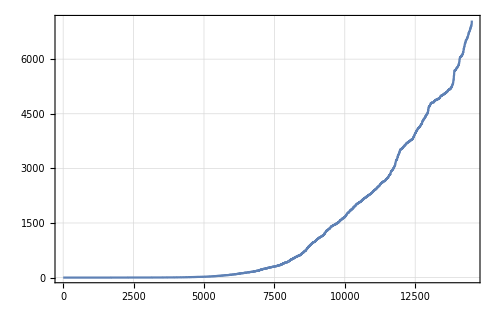

```mathematica
ListPlot[Length[#⟦2⟧]&/@csoln,
PlotRange->All,
Joined->True,
Frame->True,
GridLines->Automatic,
ImageSize->500]
```

```mathematica
remainingeqs=simp[Drop[hardeqs,25500]/.Dispatch[Take[csoln,3500]]];
```

$Aborted

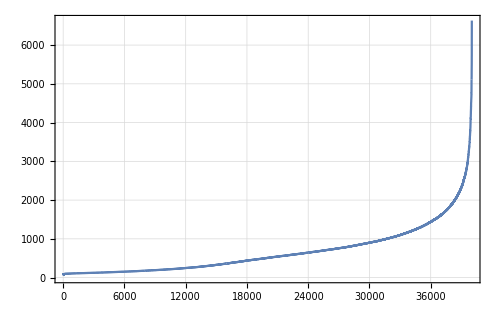

```mathematica
ListPlot[Length/@remainingeqs,
PlotRange->All,
Joined->True,
Frame->True,
GridLines->Automatic,
ImageSize->500]
```

```mathematica
Take[Length/@remainingeqs,100]
```

{58,69,69,72,75,75,75,75,76,76,76,77,77,79,81,82,82,82,83,83,83,83,83,83,83,83,84,84,84,84,84,85,85,85,85,86,86,86,86,87,87,87,87,87,87,87,87,87,87,87,88,88,88,88,88,88,88,88,88,88,88,88,88,89,89,89,89,89,89,89,89,89,89,90,90,90,90,90,90,90,90,90,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,92}

```mathematica
chunksolve[remainingeqs,csoln,10]
```

$Aborted

```mathematica
shortneweqs=simp[hardeqs⟦25501;;26500⟧/.Dispatch[newcsoln]];
```

```mathematica
Length/@shortneweqs
```

{0,0,0,0,0,0,0,0,15,344,344,883,917,1724,2190,2265,2265,2329,2460,3238,3238,4215,4948,5137,5291}

```mathematica
remainingeqs[chunksize_]:=
Module[{rheqs,chunks,dispatchtable,reqs={},neweqs},
rheqs=Drop[hardeqs,25500];
dispatchtable=Dispatch[newcsoln];
chunks=Partition[Drop[hardeqs,25500],UpTo[chunksize]];
Do[neweqs=DeleteCases[Expand[chunks⟦n⟧/.dispatchtable],0]; 
    reqs={reqs,neweqs};
    neweqs>>>neweqs.nb;Print[n,")   ", Length/@neweqs],
{n,1,Ceiling[Length[rheqs]/chunksize]}];
    SortBy[Flatten[reqs],Length]
             ]
```

```mathematica
remainingeqs[25]
```

1)   {344,2329,344,5137,15,1724,2190,2265,3238,2265,3238,883,4215,5291,4948,917,2460}

2)   {2460,253,253,4310,6549,6578,6654,5571,2430,2407,2430,2407,2430,2430}

3)   {27,7041,4,319,3557,1214,1214,2706,95,3324,3931,3931,3649,3649,4126,243,243}

4)   {3595,3595,4254,4642,2232,302,2633,2445,2632,2402,435,3124,4786,354,354,1069,1926,1926,3901}

5)   {3834,257,63,1966,68,4918,16,5,495,3478,3478,1283,321,323,1409,454,4957,4064}

6)   {6,2484,5049,2,4686,6199,5181,3088,1423,6596,4906,6345,6718}

7)   {3716,3716,337,59,296,6,1392,65,66,69,8,152,2438,2287,2781,2093,22,1667,4860}

8)   {5917,5484,1402,2,2,116,2178,2178,1082,4851,1947,1947}

9)   {1493,5013,5853,4874,493,801,1587,4294,33,1,2992,448,6,4936}

10)   {2102,1607,3418,2622,1647,1882,2175,6755,3013,26,1819,3539,1760,3276,2934,1552,5102,6371}

11)   {947,2621,958,958,247,1111,16,2217,4406,2217,1647,4074,58}

12)   {4875,3510,1498,3180,2085,5293,4,1274,1258,4884}

13)   {5977,97,3889,1410,4503,4956,2363,670,474,6}

14)   {2,5411,4889,4863,2992,1925,2934,6451,6650,104,2415,1320,620}

15)   {14,5027,18,15,6156,4801,4273,65,1744,5742,2177,47,2159,672,883,146,139,139}

16)   {3055,5021,5148,6273,6293,49,3679,7,1464,3639,4589,2332,4234,177,936,2450}

17)   {2366,2648,3794,6249,1604,3651,1819,4254,1819,24,4811,6183,4843,624,3953,3630,3,26}

18)   {3593,4816,1117,5278,32,2693,4857,1647,1,2458,836,948,1105}

19)   {4214,2886,2842,386,3511,297,1219,4340,1432,3637,2698,2698,4964}

20)   {2655,5265,2576,4806,1359,58,58,2797,33}

21)   {1817,4922,3518,5010,2179,2039,1037,896,2691,5027,317,564,1397,3397,4091,4387}

22)   {1528,83,83,83,333,1220,3851,3851,3417,3335,24,87,2148,3808,3808,3719,1335,621,2911}

23)   {3672,4834,4834,2640,3482,3482,2647,418,4426,360,360,3,3,4}

24)   {2204,4935,1322,5422,726,295,295,295,293,3,3,4,1661}

25)   {8,4215,3802,4810,1,2,18,1135}

26)   {8,37,344,548,344,120,4368,3264,2156}

27)   {278,1546,968,1099,4909,6109,5082,36,4798,5631,6388}

28)   {2561,2,2164,3,1819,597,205,209,2094,2094,115,276,3727,19}

29)   {3042,995,995,2658,4810,3759,9,20,3127,4854,6502,6502,6502,2504,5048,2760}

30)   {5048,3176,5997,6765,3759,2635,3759,5060}

31)   {337,59,1392,1423,1423,69,2578,65,110,1048,4985,1647,6154,154,1973,2283,22,2302,2219}

32)   {5677,1660,3552,4071,72,594,4}

33)   {7,21,92,7,5922,219,487}

34)   {4910,1016,8,4159,5917,8,8,69,69,6,4,2}

35)   {6385,30,6607,4032,530,1945,564,5830}

36)   {5102,5074,6663,5,5066,1343,75,4938,3506,340}

37)   {2181,4796,279,5248,46,115,1794,4045,2730,3699}

38)   {372,5003,4855,3486,1771,4201,2007,5886,7,67,115,4301,4083,5}

39)   {4637,1457,6,92,2566,3466,6721,2498,4254,18,5176,4884,5004,2951,5895}

40)   {5075,6414,6867,5055,291,3483,3592,1055,5304,2385,2531,5464,4986,4986,6365}

41)   {4921,4921,6629,6768,136,3947,3503,544,804,2405,508,1498}

42)   {826,787,515,1901,3483,3913,6428,2,6123,2,2,2,2,81,1535}

43)   {1517,3,5867,4303,2,3,205,209,1051,208,2094,2094,3939,6625,6650,2353}

44)   {205,2687,3631,6764,6290,2964,6430,48,1055,3632,2162,4599,4309,14,5134}

45)   {6164,6607,5681,2676,493,493,1791,2,2786,333,4,1335,3899}

46)   {2108,2108,2108,2906,4589,3217,3217,4957,4706,6,6,1,2,4,4,2102,2102}

47)   {2,2,2,4098,317,2125,3005,579,1,525,3}

48)   {4,2569,3915,2226,2,2,2,4214,6,6,114,3934,4280}

49)   {6,739,995,4947,118,4903,575,2504,3716,3979,1}

50)   {2730,588,2507,1227,6017,4890,280,280,4931,5747,148,4216}

51)   {4216,6435,1,12,5979,6517}

52)   {908,118,87,118,327,327,327,3724,3652,26,2408,3597,3599,3597,3599,3808,2206,4640}

53)   {2914,4834,2640,3385,3482,1820,3124,2647,2445,302,3406,6,54,357,356,357,356}

54)   {2322,295,1927,1927,34,126,40,6,3391,10,9}

55)   {19,5,5,2,4,3471,1351,622,781,4470,720,5015,474,4822}

56)   {1084,1085,1085,4854,4855,4854,1947,1920,1920,61,61,1496,1352,3909,5014,5025,5014,220,3044,3069}

57)   {6502,6502,3329,3668,3668,31,2016,1423,6,69,69,428,1039,5029,73,21,21,134}

58)   {2754,6057,5917,112,3832,20,5800,530,4214,6,560,10}

59)   {2317,3871,205,129,2096,4924,496,5165,2740,1840,4908,5396,349,1491,3593}

60)   {1110,5287,4950,2506,52,52,3692,786,4937,205,3556,3556}

61)   {2868,3007,1583,314,4908,4908,4279,69,1016,247,3069,5,4244,761,722}

62)   {205,1086,6261,2304,4306,1597,4406,4382,3200,5851,1117,314,4780}

63)   {52,6082,778,799,4268,6165,515,2061,6299,1211,4,42,12,4952,283,4,5823}

64)   {6081,4604,3532,8,4244,2466,1080,1001,2541,3466,4589,2867,4633,999,1643,4799}

65)   {2305,2181,2129,3539,5057,2982,2099,3591,5764,1465,5918,5258,826,5213}

66)   {5332,493,4843,4851,3797,1433,4589,4924,6,4936,4214,715,317,4941,2062,4024}

67)   {5601,2103,4967,6671,4455,5462,4843,4843,2241,50,2578,6027,1053,5057}

68)   {1554,4024,4088,123,1557,3705,5168,75,5511,294,6471,6123}

69)   {4867,6009,4863,4865,6217,4272,3086,1273,508,1460}

70)   {14,43,3754,25,510,4066,5335,301,4787}

71)   {2226,743,4248,4314,220}

72)   {4662,4676,5929,2918,6199,3212,6727,3643,1,4986,3604,9,3505,4297}

73)   {8,6169}

74)   {4135,2597,9,2,183,2}

75)   {2,6009,327,28,3514,3437,3561,3599,3599}

76)   {3981,1559,3597,2206,3719,418,360,6,54,356,356,3,357,3672,5066,4215,932,969}

77)   {642,4940,5106,999,3441,1656,356,2059,321,1584,16,1650,2242,3716,2939,5,10}

78)   {6434,8,28,506,3561,3383,4176,3952,3414,3221,4899,118,4396,3414,6602,3414}

79)   {3484,2597,4871,247,2613,6720,2279,3504,21,1587,4859,1615,3629,867,4985}

80)   {6057,5917,5279,2100,6,58,2,3825,20,340,340,1947,541,1496,1496,5080,1294,2664}

81)   {4814,4814,1538,4037,2317,3428,4533,1517,2369,4960,251,6139,31,1802,1047,6091}

82)   {6269,20,4635,5373,118,81,3750,6594,1552,1553,3538,2268,1465,7,2504,867,1632,2743,146,5732,36}

83)   {5496,389,5271,6123,5770,5861,4241,1579,1374,4841,2096,1167,3444}

84)   {12,803,97,4526,4839,6161,349,81,1491,1378,134,134}

85)   {36,36,40,1006,1008,19,1006,4978,1498,3577,1912,52,575,49,20,1361,20,1392}

86)   {75,340,255,4990,2019,4841,4901,24,2736}

87)   {130,1445,1445,2307,129,129,11,4983,879,1611,5978,66,69}

88)   {66,4843,5773,1572,18,2352,3069,4991,18,472,5206,3,3,205,2038,5011,6002,2972}

89)   {3,3,4271,6279,62,62,516,2220,124,228,3553,131,12,1445}

90)   {1445,2307,129,129,4,11,5787,4317,4,8,265,879}

91)   {5013,959,1107,2759,2787,1049,9,27,1202,6,42,6,12,111,111,253,253,21,62}

92)   {3509,4,5080,4800,4241,2767,543,5399,5201,4934,2892,258,999,38,2576,26,26,2385}

93)   {3727,4851,2701,3986,1001,2581,3792,3792,2117,2535,1880,4939,3611,2732,58,3539,1718,2367,3316,494}

94)   {231,5541,345,4922,1537,2252,3099,30}

95)   {5265,3547,2914,1406,1406,116,5294,4094,1294,6581,4241,4091,556,4914,1001,2243,808}

96)   {1,269,2099,931,159,1347,321,999,4633,5091,1724,3627,5,1793,89,30}

97)   {5296,422,4851,284,2964,5778,3664,5931,77,1402,3901,36,564,269,4254,4254,32}

98)   {5379,5971,358,3852,3557,3557,3557,87,4022,4102,3719,3027,418,2,455,6,935,1037,25,2138,2239,2229}

99)   {1201,330,2942,352,3441,1656,1901,356,2059,3561,6155,395,1650,3716,2097,1283,4798,2607,2037}

100)   {4032,100,2179,2,1518,1538,49,49,2,2006,2006,3,3519,3519,4825,3626}

101)   {4602,44,2969,3099,14,4,17,943,1032,1352,2741,2687,6596,3716,5796,960,40,2255}

102)   {130,130,1465,2146,16,3641,6390,2120,289,5352,645,5311}

103)   {5917,1947,14,6061,4845,5353,6155,6703,4845,6158,1374}

104)   {2232,2232,9,4782,244,3092,4831,60,3710,3608,4410,4853,3593,1294,3554,4064,115,5128}

105)   {728,665,5825,1700,1701,50,4899,5541,2747,6422,4086,263,37}

106)   {6552,1713,518,149,1204,5,110,6062,6077,5272,17,3028,3405,3361,4490,6}

107)   {1607,126,40,1385,1285,3515,2555,417,2618,2622,16,4796,3344,3282,4832,2492,4,6603,5096}

108)   {3585,5197,639,5020,40,40,3,5851,36,4865,5800,1499,6510,2807,1394,1276,243}

109)   {3595,2256,45,3797,4655,4591,3,2377,2102,4858,4847,2466,3164,531,1607,4435,14,616,63}

110)   {1966,6,18,11,286,4,2067,5,11,426,433,2618,4821,1926,4341,4940,5621,19,4924,5556}

111)   {1909,1390,5384,908,908,2365,1773,4883,6223,4085,6136,4847,4847,1353,3545,4426}

112)   {66,1878,1583,6185,3759,3088,3484,10,3517}

113)   {3124,3124,59,4575,4944,176,4866,2222,2229,557,378,3551,3562,510,1949,3646,21}

114)   {2452,1117,156,1047,2,253,4066,42,36,269,269,4851,5027,5017,4214,5089,4214,5302,7137}

115)   {6660,5013,5013,5148,5979,272,272,5853,6750,1049,9,534,5,896,1217,4041,1400,1160}

116)   {4451,4433,1600,1088,565,4522,4633,5052,496,496,1573,3059,286,2912,5541,2101,247,753}

117)   {6401,4091,298,5126,205,2281,6151,5734,5479,4150,5705,2122,2683,3676,6993,6491,2458,26}

118)   {118,83,1374,1374,3533,1446,520,2419,2419,24,3771,2897,3948,3948,192,360,4373,4526,4526,6,415,3,2}

119)   {4839,4839,4839,4839,9,1872,1161,2898,4900,4900,4025,197,2508,2912,2912,1901,344,4813,4813}

120)   {4368,2638,4854,1584,8,37,2581,2566,190,190,4839,634,5651,5651,566,4298}

121)   {2700,4909,6,4836,6466,6665,2575,2575,4856,130,999,1445,1445,1445,1445,2307,2105,2307,129,129}

122)   {129,129,11,895,4983,4983,879,879,1611,1611,3585,58,5029,1684,1684,3079,60,1213,5687}

123)   {2921,3042,6490,4843,4862,2189,3504,2972,2972,2972,2972,6359,4907,2921,2921}

124)   {3527,3621,2302,2219,3174,2794,5397,159,3679,4086,1445,5032,1526,2307,67}

125)   {141,132,2688,4,6270,2730,5265,5270,4372,5878,803,92,15,60,16}

126)   {5917,16,2866,2,74,5021,111,111,111,4873,2849,958,2225}

127)   {58,2466,2466,27,358,4022,4103,1474,6,3535,5006,2580,3,3684,384}

128)   {330,3542,3870,3542,2520,1167,8,2322,3823,3540,5335,4873,223,100,100,49,49,5081,4942,3592,4602,4044,3541,4280}

129)   {2064,53,6261,3505,5048,2915,2635,5959,20,21,3657,4478,4478,2339,135,4855,4377}

130)   {6264,3144,6561,4882,4808,2,5013,5832,5473,232,4573,4921,2761,357,303,2352}

131)   {5015,3414,3984,223,132,132,132,4208,4345,3958,40,5140,6316,3674,2904,2705}

132)   {98,3519,3887,2663,4057,261,2600,2225,738,287,4159,358,5072,4986,22,1555,3090}

133)   {5013,1,2124,3593,3369,4473,2580,3500,313,150,4870,12,133,4959,4522,4279,1700,348}

134)   {348,6002,3327,4847,3620,3620,3483,2246,3592,2511,4,638,3,487,5796,5726,4692,6607,6652}

135)   {122,493,3,1374,24,87,2148,1860,2500,4052,4052,16,3629,3629,3645,3645,2640,3871,3036}

136)   {3808,4906,6,4843,907,2743,2736,4979,4847,4860,4907,372,2382,2921,3534,333,5286,4951,1661,2520,2785}

137)   {3566,1247,16,209,37,5063,5063,5554,5124,1366,2037,2037,6755,1510,4363,1077,45}

138)   {890,4982,4982,38,4984,2800,6347,4895,122,82,1609,420,72,3,1064}

139)   {3042,3194,6316,5146,9,3127,1284,5476,6367,2310,2483,958,958}

140)   {59,1115,3887,4944,3,1577,3519,6325,559,1,85,2}

141)   {2493,1635,30,3629,15,1783,6373,803,803,4904,4910,2066,645,204}

142)   {6628,32,65,5289,4945,46,111,254,254,5579,3,5581,4,42,2,6082,2}

143)   {6812,497,2803,3851,3851,3055,3557,3335,4,4,3027,2647,2445,2397,4589,54,4888,2,1866,34,3420,4885}

144)   {6159,2316,3567,278,4932,1409,4841,5101,68,2499,5102,4757,6745,6765}

145)   {2312,2982,65,2551,2542,2126,554,3551,3907,5796,5447,137,1051,69,765,2438,2438}

146)   {2761,991,2190,59,541,541,1294,6751,6071,5677,3676,4470,1721,1294,4297,1497,2504,2522,5786,29}

147)   {4614,4434,6762,1900,2156,167,5470,293,4633,4205,5010,3724,6413,6614,2452,4801,20,624}

148)   {6688,4946,200,5057,1577,59,3610,2,4,761,2152,5369,1063}

149)   {2606,661,3848,2839,2,136,5,3259,2812,630,5278,4098,4130,3561,3561,1079,4871,37,1077,5103,5180}

150)   {2704,2868,2868,1909,1909,5082,9,3095,2831,2831,132,3593,194,1538,1338,1334,2574,4633,3611,4831}

151)   {3925,4936,3069,3069,1423,1979,2304,2304,3124,3124,1544,2837,4619}

152)   {194,194,21,949,994,2692,52,5266,5920,778,6208,2155,4214,2157,1424,1424}

153)   {5497,6272,4814,6,6649,1081,1316,1435,2224,4006,1102,1747,1981,158,344,2641,1232,3169}

154)   {1232,764,3410,6078,4119,1487,3702,1498,2350,5304,2764,5053,296,5560,1487,167,1217,3495}

155)   {6099,6067,6866,2511,954,954,1107,4,3,3,132,134,1584,4802,6760,6156}

156)   {1403,4636,2507,4314,5931,6094,1117,4,6628,3194,6081,6066,1477,2384}

157)   {3948,3948,6005,2516,1689,24,503,2447,3264,5180,3604,5634,3631,194,4336,4336,4489,6632,100}

158)   {1353,244,4789,132,4813,2721,2145,803,43,43,16,5384,2268,126,380,670}

159)   {6706,1876,6,2683,2,26,2408,3597,3599,3526,3626,3473,4052,3629,4025,2640,3871,3028,3076,3205}

160)   {54,4983,3,1225,4979,72,647,5058,4847,43,1887,1638,40,2908,1006,1008,4,4,164,4813}

161)   {3822,3449,55,52,49,4365,2639,999,599,4818,2}

162)   {5063,5011,2656,4854,4855,4854,1085,5027,5033,4982,4982,5017,5018,72,650,5365,274,242,5061,5061}

163)   {4847,6237,75,69,1793,3556,120,1580,1586,1580,5825,270,61,3507,66,3044,3069,85,85,6497,4885,2519,2519}

164)   {6492,3129,2975,3821,237,2730,3,2304,1917,1413,2548,2548,4944,4944,4945,1329,293}

165)   {26,5005,6669,4752,4999,3467,1832,638,1772,3507}

166)   {8,4378,21,671,3529,6875,1474,665,10,5821,4963,5341,2338,2338,5246,1084,4855}

167)   {32,1496,6229,6,6840,22,6067,6057,2,541,5267,6964,2386,3999,4642,4642,4529,4220}

168)   {3086,1228,1689,3742,2576,4547,1834,1945,5218,5265,2369,3006,6217,96,6097,4051,348}

169)   {5541,4945,358,962,1261,645,1351,1048,1144,585,5826,356,356,6629,6014,140,140,494,1719}

170)   {4062,4846,4846,1520,4529,4529,2812,3721,2169,191,4843,4843,3096,4194,3092,1559,1559,1110,3715,1912,4942,368,4804}

171)   {4024,2311,1179,6721,1068,1445,1445,1445,2307,2315,129,129,241,6625,3,3,4958,4958,122,1613,1550}

172)   {1613,75,66,3556,1151,6288,1068,2150,1752,151,2876,6183,177,3532,3532}

173)   {3597,4323,1584,1247,6546,5,6550,6063,776,487,2277,2277,3578,5027,3524}

174)   {111,111,5268,4992,5272,6568,198,2157,2408,1981,3466,1700,1037,3871,3259,1378,40,3623,1881,173}

175)   {2039,1431,1247,3884,15,4875,4,533,4771,2612,2542,4248,5761,5165,1432,2204,5083}

176)   {4837,5592,6625,26,1427,15,1401,5,15,1373,10,571,2945,10,6656,5990,403,2780,3660,5987}

177)   {1274,1272,6,5049,2650,6129,6,1698,6647,6,514,630,5777,661,3797,417,5259,4,5,2812}

178)   {4093,4098,36,4870,5631,5134,2704,6754,62,2786,5323,3095,2,2166}

179)   {2578,4512,29,3749,1690,1472,3069,3069,1217,2912,1801,4211,4977,4803,6,2220,2805,5829}

180)   {124,1463,4833,4855,5013,2242,4802,1422,3,2504,4094,4094,67,4986}

181)   {2,41,41,6705,3,5748,1533,303,303,3514,1439,3662,3662,3662,3541,2245,2245,2245,2245,2300,3810,4254,3797,3027}

182)   {3604,2700,2633,2944,2944,3250,3250,3672,3672,4834,4834,5,24,4981,5823,297,297,932,1637,653}

183)   {40,3441,1656,1632,356,4013,2059,321,1650,368,3716,1337,1337,1642,4934,1337,3727,3633}

184)   {2177,2177,1082,4852,1734,1348,2156,5472,5893,2802,2802,6632,1186,3177,2788,3422,1352,1352,6602,1543,6343,2747}

185)   {6118,3200,4554,2910,3877,5783,6732,115,1583,4855,181,181,3614,4,5752,2643,255}

186)   {255,255,7,7,7,2,2,2,6,2369,3829,3829,2661,3829,5,5,484,484,2090,373,126}

187)   {40,544,254,4214,4818,6777,1424,1719,3561,3599,1559,3597,2109,1560,3645,726,293,4534,4309}

188)   {2020,634,1312,1347,1670,115,5332,4989,1022,3970,341,341,1650,554,5036,6582,4098}

189)   {2541,4063,2931,420,325,120,1580,270,3,1862,1586,1583,2452,3221}

190)   {2304,3414,151,1543,2380,5286,3648,236,4614}

191)   {2747,14,43,3907,2876,33,5817,5585,2272,4564,58,12,12,5,4958,2342}

192)   {22,7,30,1947,6558,6672,5314,13,272,274,13,274,2664,6767,511,836,2957,2475,2573,5850}

193)   {3886,2341,2500,313,3547,4940,205,6,3076,4824,565,4419,4419,6182,2090,3027,1573,4887,2755,149}

194)   {2214,4880,5743,6062,4103,2962,1896,936,134,3962,1315,4855,1944,1927,3091,1286,2166,5462}

195)   {656,1068,2181,2150,156,4847,258,261,2337,1117,6156,3590,124,4967,70,3033,4526,2195}

196)   {1855,1130,2046,5352,6039,2222,5022,5472,6,5352,4255,4279,3154,3903,2730,6660,1167,5755,1186}

197)   {1364,2599,6684,4297,2395,71,6310,7237,6778,5852,67,562,13}

198)   {3797,3797,2663,360,1037,807,4839,4839,3469,3469,4900,4198,4900,1921,3804,6112,532,4}

199)   {3416,40,1178,352,1336,2596,2547,548,3671,148,5146,1085,4854,1949,2375,5783,2166,1945,4983}

200)   {4176,4431,4431,205,1611,2533,1994,1999,3,296,6183,12,20,44,4945,1947,2972,2972}

201)   {122,264,2066,345,4222,3483,2124,24,3467,4850,5772,6550,4071,4974,92,741}

202)   {803,803,803,983,4103,4194,329,4985,5063,6435,3873,111,1080,4844,1488,2565,3676}

203)   {3998,4529,3886,1595,779,2466,1804,1919,4102,4,804,1459,5,6,4855,6120,1125,1609,531,1926}

204)   {19,4924,5556,5025,5025,2646,6593,4905,4905,6333,6717,6333,6717,3666,3666,1583,1734,2578,5470,5031,1878}

205)   {3191,283,3929,2533,2630,3258,3871,2650,3088,6517,5086,6616,3124}

206)   {3124,3662,296,6,1392,5011,8,10,2222,2229,2807,2820,498,3483,3700,557,378}

207)   {2049,5265,246,5818,4882,4094,6,1947,1947,6998,5013,5235,5853,1876,87}

208)   {4847,991,944,2614,321,562,3248,2,4857,1860,1860,1670,5332,4989,3970,341,341,1650}

209)   {554,5025,5025,151,3946,2590,2179,2179,2612,4847,81,13,420,1,5761,5761,275}

210)   {1029,4158,3202,5905,1213,4,2504,2972,5366,242,3405,3369,2662,6292,624}

211)   {1544,2268,3648,4086,4855,6749,4806,5260,30,4910,4142,15,3904}

212)   {2003,3513,3748,4958,4847,2342,5986,5013,4386,3676,6574,2580,3163,4860}

213)   {1788,3500,6,3634,4255,251,6204,13,2246,6674,1733,6578,354,2375,3903,1222,3451,5048,3527,1681}

214)   {3774,5005,3946,4025,4811,3785,6653,6572,5977,1651,1536,4017,4017,4591,3417}

215)   {4839,4839,4900,3662,4902,1347,251,1498,4917,4379,1080,1080,882,4983,818,205,1611,4644,3494}

216)   {1064,25,3666,3076,2124,2972,2972,2687,5430,615,6727,6551,255,281,1463,794,4850,4,4807}

217)   {2298,204,113,340,6586,1207,111,4872,4872,14,207,50,5078,6373,13,303,3632,3855,3855,3557,3557,3611}

218)   {3611,87,3832,1750,3027,3285,2652,2,380,380,4548,4548,4507,3535,606,4847,1713,1713,1706,1706,40}

219)   {3458,1080,1080,4844,4844,1669,1947,18,18,1645,1488,1488,717,5019,5019,1045,3566,2614,4856,2102,3191}

220)   {2997,6113,5324,2560,251,251,5323,5327,1347,2622,4870,454,1283,3183,2592,2176,1112,1097}

221)   {4854,4861,1408,1550,241,4816,5768,3723,4847,4907,825,5893,5438,4,329,2700,5947,6683,6596}

222)   {6727,1392,217,3,3562,5717,1741,3464,4852,1533,4799,639,5751,864,24,280,2877,56,5283,20}

223)   {2704,16,2087,4,1459,6800,210,1465,255,7,114,4386,4008,3797,3797,3797,2985,2653,3005,3005,4526}

224)   {6116,3999,1510,3405,2651,3606,4940,5020,3985,6401,2,5769,2493,4084,106,25,5223,3763,5021}

225)   {2704,156,5725,5992,2718,6005,6394,6522,25,3416,564,2298,923,4844,4226,1960,2422}

226)   {3131,1025,2242,5658,4908,5073,6927,4250,1661,4842,3476,296,6190,1791,4790,811,3686,5739,4844,2268,803}

227)   {1019,2286,269,3839,5,228,6653,303,6236,1041,24,3797,2083,2083,3629,3629,3756,3756,5050}

228)   {1555,2768,2206,2983,1117,6,40,2797,2683,2668,4860,5297,1438,3643,3601,3629,3629,2785,6118,3461,5276}

229)   {4215,2638,4031,3874,1315,2521,42,42,3102,1230,6127,2569,1048,4349,5063,5063,5063,2706,5309,5121}

230)   {5554,4676,3,5225,79,6369,5927,5927,6508,6508,6508,5101,6916,6765,6765,2179,5328,2571,6241,5197,242,4803,81,3958}

231)   {5167,420,2894,5140,4499,3789,325,66,278,1026,1686,2704,228,1068,3194,3042,3194,5138,122,3127,5000,3042,5117}

232)   {1752,4913,3163,5920,2310,5838,1423,1423,1392,1577,4828,4349}

233)   {3604,2218,40,5863,1247,1184,5213,2572,21,7,30,5265,2890,6738,553}

234)   {778,4295,543,2440,454,135,48,4215,5706,5292,42,4096}

235)   {15,46,1945,6585,6658,5042,218,218,6659,35,6788,5587,5267,3033,5071,209,798,2102,993}

236)   {503,3506,5232,5095,283,6385,3486,1924,5910,205,6517,4851,5985,5872,5715,6130,58,4355,6732,4884,3767}

237)   {1537,5839,5376,3246,2374,58,58,4020,4472,3284,3032,1490,1490,296,287,2,1316,1635,152,228,753,525}

238)   {4127,85,1433,321,4901,6581,3441,1659,3486,3666,70,2378,3085,38,5659,1698,3732,3967,3954,5182}

239)   {6159,2719,4372,5802,215,6580,964,5254,6173,1029,5020,1459,111,2718,132,1011,163,31,4965,4870}

240)   {5791,4928,258,530,3923,3592,2357,2896,31,907,5155,5201,5194,5201,5194,42,2268,1965,4713,1646}

241)   {503,4868,6589,6158,1487,4963,1098,2,81,1535,1517,3,1725,205,209,2094}

242)   {2094,2849,5011,5762,6099,3693,3592,15,1857,10,5194,1643,6727,6727,573,3527,170,2970,2616}

243)   {4308,2,2730,6,5017,2853,4533,3767,6,803,6001,6,356,1947,85}

244)   {2548,3746,3,3438,3417,4113,3797,2816,251,4089,42,1526,3041}

245)   {5156,2602,4379,1077,2761,886,4984,817,1609,2949,209,129,5836,2969,6043,3919,3517,723}

246)   {2219,4988,2,5911,83,83,1531,204,5801,204}

247)   {3827,4035,912,2491,6904,6902,111,2680,5517,127,4091,3541,4037,4002,1517}

248)   {1981,4,4,4946,4946,3673,4932,1286,6289,3122,2103,700,1564,3760,60,6550,3948,2576,3763,5791}

249)   {5897,4932,4616,484,6561,6576,2061,261,2372,4,4423,3277,345,4860,4470,1901,3534,612,3700,2943,1733}

250)   {1174,262,5283,5554,1487,2649,6278,6508,536,66,6347,4374,120,3647,6649,5968,1419,5197,3132,2635,2635}

251)   {3584,1164,4847,4847,3701,2030,70,1878,554,5159,296,1692,3466,5469,198,1057}

252)   {5688,284,2120,42,6518,2578,1564,220,220,2298,2083,3629,3756,4548,4548,4688,4923,1706,1706,4307}

253)   {4098,4093,4100,10,3411,42,1398,6112,1926,1230,6120,4871,4854,532,4871,21,5063,5063,5011,5011,1707}

254)   {6508,6508,6612,3753,3753,2535,1504,1111,4861,1920,1550,1550,1947,1920,4816,4816,5013,5013,5024,5236,5236,5768}

255)   {5768,3723,3723,5470,4832,2897,1852,2536,2527,2732,5100,2509,3044,3069,3129,3465,5947,5947,3129}

256)   {5947,5947,2304,1423,6,4828,5011,2703,50,869,2225,71,4855,4799,2690,16,3507,8,4963,5271}

257)   {5265,5270,671,4332,4332,6413,2212,569,48,3829,18,4,1654,2442,514,6812,1037,1555,4347}

258)   {406,721,1697,2797,2683,3721,2578,1438,3643,2930,6111,6118,6116,5276,5272,3979,32,37,2592,2592}

259)   {6366,6369,6366,2035,6138,241,5195,2933,3020,712,712,2296,129,129,129,5959,4851,4851,1752,4873,1752,1947}

260)   {5128,5652,2897,6435,4988,124,3997,1326,2572,5153,6276,3593,5268,5268,18,2061,6904,59}

261)   {3740,6785,6805,1564,4476,995,1728,2460,2460,3860,1080,2020,4019,4249,2303,540,2354,2913}

262)   {1881,1542,5027,1406,5864,2686,5365,215,864,879,16,361,6276,1564,6034,4058,4334,4718}

263)   {1947,3932,3814,1949,285,3555,4871,1756,3506,276,6351,3625,3733,4158,1207,1219,1219,1376,360,6190,81,6099}

264)   {5796,652,652,13,4087,1878,5332,8,3416,3254,6374,6229,856,3985,4732,520}

265)   {4393,2019,3813,4573,3779,5164,999,6180,6180,1433,4254,6210,215,2302,4526,261,1721,591}

266)   {6389,2629,5770,4902,6964,495,1490,1034,1651,2834,3776,4,4,3940,4841,1374,3797,2910,3076,973,3419}

267)   {4924,4924,4526,406,1999,5209,5198,5209,5198,5,2213,4936,369,1834,2580,3630,2639,1254,3875,999,135,3555,4841,2065}

268)   {313,2533,2533,1743,3722,5094,4986,26,6,3833,5122,5015,2607,3942,2536,2536,3798,6508,999,1498,1498,2350}

269)   {2350,129,129,5294,2489,5349,2669,1518,1518,6167,818,1611,1611,1338,3775,120,3,433,2268,6184,5893,2357}

270)   {1743,207,90,2250,5018,5018,3028,2504,1220,3018,2902,218,4820,5834,8,8}

271)   {2804,1259,6337,2665,5802,5003,2237,4,6776,484,1601,488,3638,294,5388,6002,6001,6002,6000}

272)   {6001,205,579,15,5286,40,204,5917,198,4855,340,1009,5566,111,111,274,5273,220,2145,22,3904,5363,1456}

273)   {1315,1082,4852,2,2,99,4862,13,4874,51,6347,1098,4160,4591,1721,3543,1951,1791,753,5472,1418,1338}

274)   {6274,540,540,1701,4999,2859,2834,3689,2304,6347,4860,2637,2375,1695,4982,92,385,32,67,3019,4862,4894,4894,1001}

275)   {4466,4589,5267,5050,4263,4025,2930,2930,3277,1661,1347,404,4957,5472,2059,2310,3716,4108,3993}

276)   {6127,4098,6,5265,6604,6908,4856,2535,2378,4814,390,6279,6626,5267,3486,5317,2527,3079,2732,3732}

277)   {3712,2536,1167,2452,6461,3221,3594,2304,6417,1377,2261,3522,6353,3630,4}

278)   {3608,118,205,5104,5090,5,6196,5043,3466,6605,6085,3416,5236,4096,5236,2664,6569,4361,3756,3074}

279)   {4377,3217,6,1721,2689,2436,1312,1784,45,4854,3554,3,536,5792,5761,744,5447,5835,2067,902,6}

280)   {2616,6463,761,6,7,6022,1469,1525,4571,5989,146,1721,771,2339,3797,2710}

281)   {2579,1125,10,20,3291,12,426,6,7041,5928,5928,6379,122,278,4595,5896,2510,2510,2507,5251,4857,4238,4906}

282)   {6718,1139,258,5764,6287,5420,378,557,5044,44,2012,2188,52,169,6550,6550,741,4810,5268}

283)   {5727,6222,5471,4099,3557,1471,3964,4020,415,1687,2317,34,3548,3777,1946,2857,2315,1172,374,6368,6401,2892,4820}

284)   {4248,5791,10,6258,5272,6002,2225,142,142,6109,2108,2812,6794,3020,4819,2655,2551,2667,194,348}

285)   {1663,255,1047,7,5024,2,122,4903,3829,91,5,484,6650,4870,6748,3541,2245,2245,2245,2300,1711,4507}

286)   {3823,1812,4052,2,3645,3645,4397,3472,357,303,2,6139,1304,1313,1670,5325,4988,3970,2101,341,341,1650}

287)   {554,1135,1852,4098,4935,999,1378,4852,3986,5858,6849,5329,671,2,266,266,5893,2876,2354,2406,3252}

288)   {3252,5192,5914,5761,2192,20,3177,2103,2200,242,242,2504,6596,2108,2108,2108,3667,5198,4944}

289)   {1256,2937,132,4025,4945,3643,2277,4855,3626,348,6022,2757,1499,7,7,7,44,6383,10}

290)   {52,5,5,442,739,40,4,61,6672,6988,3768,3266,4438,3797,1434,6408,531,3871,4921,2586,1932,2930,1617}

291)   {377,313,313,4843,1056,4097,333,5259,1660,283,850,781,5172,6897,3770,4526,35,4098,803,315}

292)   {6,2525,5955,2761,6582,5078,1434,4800,5853,1329,1331,6062,2827,241,1860,4526,1185,6306,1160,6112,4098,5412}

293)   {3813,5613,4023,3561,4364,1579,2666,3555,129,129,4227,4785,744,4794,6709,1606,3076,5757}

$Aborted